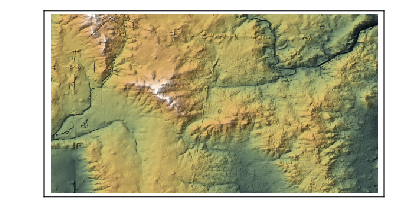

```mathematica
img=Import["http://exampledata.wolfram.com/ArcGRID.zip","ARCGrid"]
```

Import the data files, which is a 299 by 554 matrix.

```mathematica
data=Import["http://exampledata.wolfram.com/ArcGRID.zip",{"ARCGrid","Data"}];
```

```mathematica
{m,n}=Dimensions@data
```

{299,554}

```mathematica
data//Short[#, 10]&
```

{{216.207,216.082,215.93,215.692,215.464,215.323,215.247,215.255,215.125,214.984,214.856,214.623,214.395,214.048,213.713,213.566,213.354,213.254,213.254,213.254,213.254,213.15,213.141,212.828,212.518,212.339,212.154,212.054,211.979,211.957,211.854,211.946,«491»,212.1,211.875,211.795,211.795,211.795,211.739,211.795,211.795,211.845,212.01,212.082,212.674,212.889,213.046,213.331,213.445,213.543,213.382,212.816,212.297,211.811,211.795,211.795,211.795,211.795,211.795,211.795,211.795,211.795,211.795,211.795},«297»,{«1»}}

Get the longitude and lattitude of the area.

```mathematica
{lat,long}=Import["http://exampledata.wolfram.com/ArcGRID.zip",{"ARCGrid","SpatialRange"}]//QuantityMagnitude
```

{{40.0617,40.1447},{-88.3158,-88.1619}}

So the area stored in the ArcGrid file is for area with lattitude 40.0617 to 44.1447, and longitude -88.3158 to -88.1619. This area is futher divided into uniform cells, and there are totally 554 cells in each row, and 299 cells in each column. We then compute the stepsize along the x and y-axis.

```mathematica
{ystepsize, xstepsize}={(lat[[2]]-lat[[1]])/m, (long[[2]]-long[[1]])/n}
```

{0.000277778,0.000277778}

```mathematica
SeedRandom[1234];
```

Supose we want to get all the cells for the area with lattitude 40.0688 and 40.0931, longitude -88.2355 and -88.1809.

```mathematica
{left,right}=Sort@RandomReal[long,2]
```

{-88.2355,-88.1809}

```mathematica
{bottom,top}=Sort@RandomReal[lat,2]
```

{40.0688,40.0931}

Since these boundary values does not necessary coincide with the boundary of cells, we will get the smallest rectangle covering the rectangle area.

```mathematica
leftindex=Floor[(left-long[[1]])/xstepsize]
```

289

```mathematica
rightindex=Ceiling[(right-long[[1]])/xstepsize]
```

486

```mathematica
bottomindex=Floor[(bottom-lat[[1]])/ystepsize]
```

25

```mathematica
topindex=Ceiling[(top-lat[[1]])/ystepsize]
```

113

After computing the index of the boundary cells, we compute the actually coordinates.

```mathematica
left2=long[[1]] + leftindex * xstepsize;
```

```mathematica
right2=long[[1]] + rightindex * xstepsize;
```

```mathematica
bottom2=lat[[1]] + bottomindex * ystepsize;
```

```mathematica
top2 = lat[[1]] + topindex * ystepsize;
```

```mathematica
grid=Graphics[{Opacity@0, EdgeForm@Black, Rectangle[{left2,bottom2},{right2,top2}]}]//Show[#, PlotRange->{long,lat}]&;
```

The area in the rectangle in the figure below are the area which we are interested.

```mathematica
Overlay[{img,grid}]//Magnify[#, 2]&
```

-Graphics--Graphics-

```mathematica
{zmin,zmax}=Import["http://exampledata.wolfram.com/ArcGRID.zip",{"ARCGrid","ElevationRange"}]//QuantityMagnitude
```

{205.912,243.102}

```mathematica
cf=ColorData["GreenBrownTerrain"] @* (Rescale[#,{zmin,zmax},{0,1}]&);
```

We can plot the reliefplot of the values:

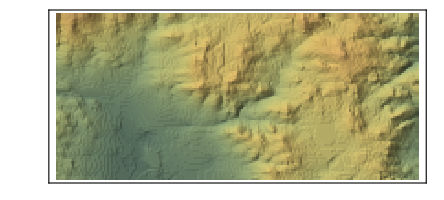

```mathematica
data[[bottomindex;;topindex, leftindex;;rightindex]]//ReliefPlot[#,ColorFunction->Function[{z},cf[z]], ColorFunctionScaling->False]&
```